```mathematica
γ[θ_,λ_]=Cos[λ]{Cos[θ],Sin[θ],0}+{1,1,Sin[λ]}
```

{1+Cos[θ] Cos[λ],1+Cos[λ] Sin[θ],Sin[λ]}

```mathematica
ParametricPlot3D[γ[θ,λ],{θ,0,2π},{λ,0,π},PlotStyle->{Black,Opacity[.7]},MeshStyle->{White}]
```

-Graphics3D-

#### Paraboloide

```mathematica
ψ[r_,t_]:={r Sin[t],r Cos[t],r^2};
```

```mathematica
paraboloide=ParametricPlot3D[ψ[r,t],{r,0,3},{t,0,2π},PlotStyle->{Opacity[.1],Gray},PlotPoints->100,MeshStyle->{{Thin,Gray},{Thin,Gray}}];
```

```mathematica
circs =Table[ParametricPlot3D[ψ[ρ,t],{t,0,2π},PlotStyle->{Green,Thick}],{ρ,2,2.5,.5}];
```

```mathematica
mers=Table[ParametricPlot3D[ψ[ρ,t],{ρ,0,3},PlotStyle->{Green,Thick}],{t,π/6,π/3,π/6}];
```

```mathematica
placaIn=ParametricPlot3D[ψ[ρ,τ],{ρ,2,2.5},{τ,π/6,π/3},PlotStyle->{Purple},Mesh->None];
```

```mathematica
placaOut=ParametricPlot3D[{(ρ+.3) Sin[τ],(ρ+.3) Cos[τ],(ρ+.3)^2-1.5},{ρ,2,2.5},{τ,π/6,π/3},PlotStyle->{Red},Mesh->None];
```

```mathematica
Show[paraboloide,circs,mers,placaOut,placaIn]
```

-Graphics3D-

#### Exemplo 4 - Página 163

Campo conservativo F = P i + Q j, onde P e Q dependem de x e y. No StreamPlot podemos escrever

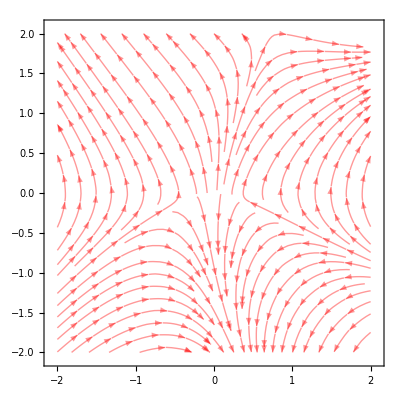

```mathematica
fieldEx4=StreamPlot[{6x y-y^3,4y+3 x^2-3x y^2},{x,-2,2},{y,-2,2},StreamStyle->{Opacity[.4],Red}]
```

#### Função Potencial

A condição ∂P/∂y = ∂Q/∂x é satisfeita, pois

```mathematica
D[6x y-y^3,y]===D[4y+3 x^2-3x y^2,x]
```

True

Fazendo ∂f/∂x = P(x, y), onde f é a função potencial, temos que

```mathematica
f1=Integrate[6x y-y^3,x]
```

3 x^2 y-x y^3

f1 ainda possui uma função de y como “constante” da integração anterior. Derivando f1 com relação a y e igualando ao valor de Q(x, y) (∂f/∂y), vem

```mathematica
d1=D[f1,y]
```

3 x^2-3 x y^2

```mathematica
Solve[d1+c1 ==4y+3 x^2-3x y^2,c1]
```

{{c1→4 y}}

Como c1 é a derivada de uma função de y, para obter essa função

```mathematica
int1=Integrate[4y,y]
```

2 y^2

Logo, ao acrescentar o termo obtido em f1, temos

```mathematica
f[x_,y_]=f1+int1
```

3 x^2 y+2 y^2-x y^3

```mathematica
contourEx4=ContourPlot[f[x,y],{x,-2,2},{y,-2,2},ContourShading->False,Contours->20,ContourLabels->True];
```

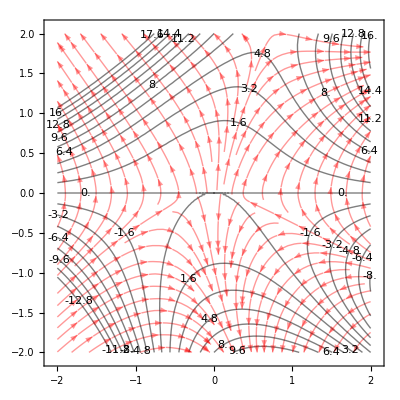

```mathematica
Show[fieldEx4,contourEx4]
```

```mathematica
ContourPlot3D[z==3 x^2 y+2 y^2-x y^3,{x,-2,2},{y,-2,2},{z,-10,10},ContourStyle->{Opacity[0.7],Red},BoundaryStyle->Magenta,Mesh->None,PlotPoints->100]
```

-Graphics3D-

-Graphics3D-

```mathematica
ContourPlot3D[z==3 x^2 y+2 y^2-x y^3,{x,-2,2},{y,-2,2},{z,-10,10},ContourStyle->{Opacity[0.7],Red},BoundaryStyle->Magenta,Mesh->None,PlotPoints->100]
```

-Graphics3D-

-Graphics3D-

## 16.3 Problemas

Questão 1) Baseando-se no que foi visto no exemplo 4 acima, para o campo vetorial F(x, y) = (2x + 3y) i + (3x + 2y) j, temos que a condição ∂P/∂y = ∂Q/∂x é satisfeita. Dessa forma, admitindo que f(x, y) = Integrate[P(x, y), x], obtemos

```mathematica
f2=Integrate[2x+3y,x]
```

x^2+3 x y

```mathematica
x^2+3 x y (* A função arbitrária dependente de y não está sendo contabilizada, mas vai ser obtida. *)
```

x^2+3 x y

De forma análoga a anterior, vem

```mathematica
Solve[3x+c2==3x+2y,c2]
```

{{c2→2 y}}

Integrando c2 = D[f(y), y]

```mathematica
Integrate[2y,y]
```

y^2

Somando a f(x, y) chegamos na seguinte função potencial

```mathematica
ff[x_,y_]=x^2+3y x+y^2
```

x^2+3 x y+y^2

O campo vetorial do enunciado no StreamPlot torna-se

```mathematica
field1=StreamPlot[{2x+3y,3x+2y},{x,-2,2},{y,-2,2},StreamStyle->{Opacity[.4],Red}];
```

Função potencial graficamente

```mathematica
contour1=ContourPlot[ff[x,y],{x,-2,2},{y,-2,2},ContourShading->False,Contours->20,ContourLabels->True];
```

Juntando os dois

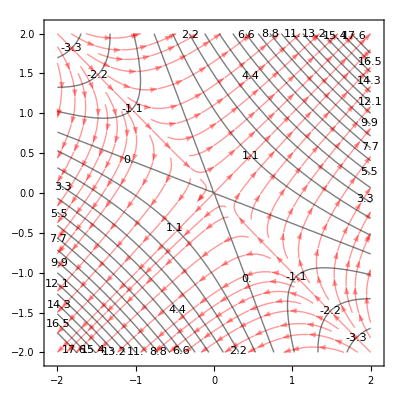

```mathematica
Show[field1, contour1]
```

Questão 2

Campo vetorial do enunciado no StreamPlot

```mathematica
stream2=StreamPlot[{4x-y,6y-x},{x,-2,2},{y,-2,2},StreamStyle->{Opacity[.4],Red}];
```

Seguindo o mesmo procedimento anterior a função potencial será f(x, y) = 2 x^2-yx+3 y^2. No ContourPlot

```mathematica
contour2=ContourPlot[2 x^2-y x+3 y^2,{x,-2,2},{y,-2,2},ContourShading->False,Contours->20,ContourLabels->True];
```

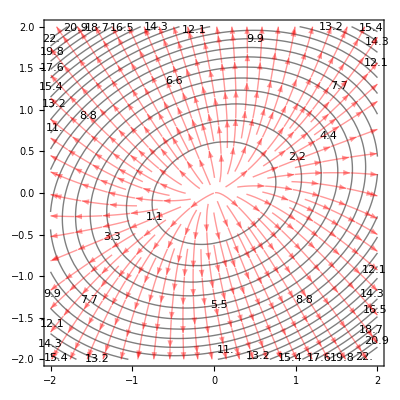

```mathematica
Show[contour2,stream2]
```

Questão 3

```mathematica
stream3=StreamPlot[{3 x^2+2 y^2,4x y+6 y^2},{x,-2,2},{y,-2,2},StreamStyle->{Opacity[.4],Red}];
```

```mathematica
Grad[{3 x^2+2 y^2,4x y+6 y^2},x,y]
```

Grad[{3 x^2+2 y^2,4 x y+6 y^2},x,y]

```mathematica
Grad[{3 x^2+2 y^2,4 x y+6 y^2},x]
```

{3 x^2+2 y^2,4 x y+6 y^2}x

```mathematica
contour3=ContourPlot[2x y^2+2 y^3+x^3,{x,-2,2},{y,-2,2},ContourShading->False,Contours->20,ContourLabels->True];
```

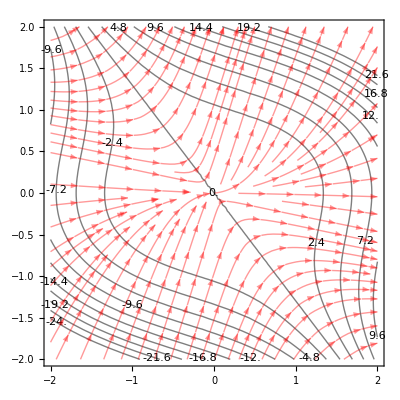

```mathematica
Show[contour3,stream3]
```

Questão 15

```mathematica
stream15=StreamPlot[{3 x^2 y^3+y^4,3 x^3 y^2+y^4+4x y^3},{x,-2,2},{y,-2,2},StreamStyle->{Opacity[.4],Red}];
```

```mathematica
contour15=ContourPlot[x^3 y^3+x y^4+y^5/5,{x,-2,2},{y,-2,2},ContourShading->False,Contours->20,ContourLabels->True,PlotPoints->100];
```

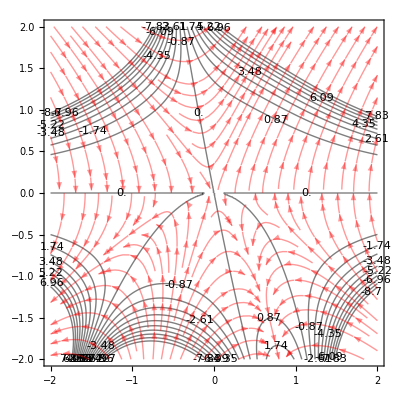

```mathematica
Show[contour15,stream15]
```

```mathematica
ContourPlot3D[z==x^3 y^3+x y^4+y^5/5,{x,-2,2},{y,-2,2},{z,-8,8},PlotPoints->100,MeshFunctions->{#3&},ContourStyle->{Opacity[0.4],RGBColor[0.67,0.08,1]},MeshStyle->{{Blue,Thick},{Blue,Thick}}]
```

-Graphics3D-

Exercício 26

```mathematica
stream26=StreamPlot[{-y/(x^2+y^2),x/(x^2+y^2)},{x,-1.7,1.7},{y,-1.7,1.7},StreamStyle->{Opacity[.4],Red}];
```

```mathematica
D[-y/(x^2+y^2),y]===D[x/(x^2+y^2),x] (* Campo não conservativo *)
```

False

```mathematica
ω[t_]={Cos[t],Sin[t]};
```

```mathematica
γ[t_]={Sin[t],Cos[t]};
```

```mathematica
path261=ParametricPlot[ω[t],{t,0,π},PlotStyle->{Red,Thick}];
```

```mathematica
vv261=Graphics[Table[{Red,Thick,Arrow[{ω[κ π/6],ω[κ π/6]+.5ω'[κ π/6]}]},{κ,0,1.7π}]];
```

```mathematica
vv261f=Graphics[Table[{Green,Thick,Arrow[{ω[κ π/6],ω[κ π/6]+.8ω'[κ π/6]}]},{κ,0,1.7π}]];
```

```mathematica
path262=ParametricPlot[{Cos[t],Sin[t]},{t,0,-π},PlotStyle->{Blue,Thick}];
```

```mathematica
vv262=Graphics[Table[{Blue,Thick,Arrow[{γ[κ π/6],γ[κ π/6]+.5γ'[κ π/6]}]},{κ,Pi,2.8Pi}]];
```

```mathematica
vv262f=Graphics[Table[{Green,Thick,Arrow[{ω[κ π/6],ω[κ π/6]+.8ω'[κ π/6]}]},{κ,2.2π,3.7π}]];
```

```mathematica
points=Table[Graphics[{PointSize[Large],Purple,Point[{{κ,0}}]}],{κ,-1.,1.,2}];
```

```mathematica
label=Graphics[{Purple,Text["Início",{1.5,0}]}];
```

```mathematica
label1=Graphics[{Purple,Text["Fim",{-1.5,0}]}];
```

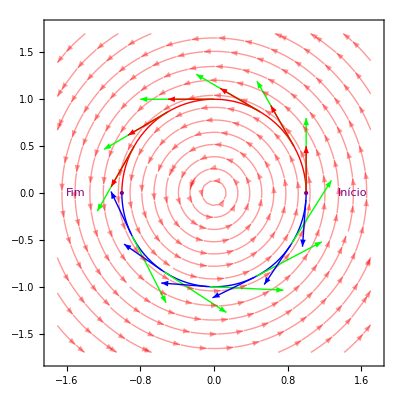

```mathematica
Show[stream26,path261,path262,vv261f,vv262f,vv261,vv262,label,label1,points]
```